Pulse interleaved excitation (PIE)  and  Alternating-laser excitation (ALEX)

PIE settingspaclet:Fretica/tutorial/PulseInterleavedExcitationPIEAndAlternating-LaserExcitationALEX#208260038 | Analyzing PIE datapaclet:Fretica/tutorial/PulseInterleavedExcitationPIEAndAlternating-LaserExcitationALEX#152825062
PIE channels selectionpaclet:Fretica/tutorial/PulseInterleavedExcitationPIEAndAlternating-LaserExcitationALEX#31195577 | “BurstPIEAsymmetry”, FPIEBurstAsymmetry,  FPIECutAsymmetricBurstspaclet:Fretica/tutorial/PulseInterleavedExcitationPIEAndAlternating-LaserExcitationALEX#176400191

```mathematica
Needs["Fretica`"]
```

PIE settings

```mathematica
?FEnablePie
?FSetPIERoutes
```

```mathematica
FSetFRETRoutes[{"A","D","A","D",0,0}];

FEnablePie[True];
FSetPIERoutes[FGetAcceptorRoutes[]]
```

{1,0,1,0,0,0}

```mathematica
?FSetAnisotropyRoutes
```

```mathematica
FSetAnisotropyRoutes[{"P","S","P","S"},{"P","S","P","S"}]
```

```mathematica
FGetAnisotropyRoutes[]        (* settings for donor-excitation laser *)
FGetPIEAnisotropyRoutes[] (* settings for acceptor-excitation laser *)
```

{P,S,P,S,0,0}

{P,S,P,S,0,0}

PIE channels selection

```mathematica
SetDirectory[$FreticaExamples];
FOpenTTTR["RhoK_5M_30min_a.t3r"];
```

```mathematica
FLifeTimeHisto[FRoutes->{1,2},FPhotonData->All]
```

-Graphics-

```mathematica
FPIEChannelSelector[{1,2}]
```

```mathematica
FGetChannelConstraints[]
FGetPIEChannelConstraints[]
```

{{1823,2582},{1823,2582},{1823,2582},{1823,2582},{1823,2582},{1823,2582}}

{{2640,3466},{2640,3466},{2640,3466},{2640,3466},{2640,3466},{2640,3466}}

```mathematica
FSetChannelConstraints[chmain={1832,2599}]
FSetPIEChannelConstraints[chpie={2653,3456}]
```

{{1832,2600},{1832,2600},{1832,2600},{1832,2600},{1832,2600},{1832,2600}}

{{2653,3457},{2653,3457},{2653,3457},{2653,3457},{2653,3457},{2653,3457}}

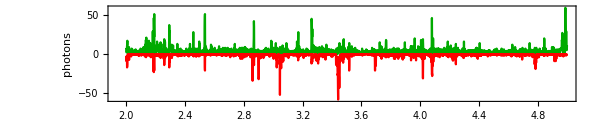

```mathematica
FMCStrace[{{{1,1,1,1},chmain},{{1,0,1,0},chpie}},1.,2,5.,Weights->{1,-1},PlotStyle->{Darker@Green,Red}]
```

Analyzing PIE data

4093

{1030.48,2373.97,17.1608,14.6691,0.,0.}

{912.801,35.1782,17.6911,15.0809,0.,0.}

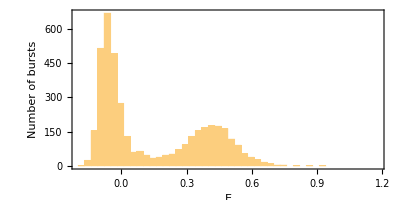

```mathematica
FFindBurstsDeltaT[0.00015,50,10000];
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,50,10000]
FDetermineBackground[]
FGetPIEBackground[]
FParamHisto["E",{-0.2,1.2,0.03}]
```

```mathematica
?FSetPIEBackground
?FGetPIEBackground
```

```mathematica
?FSetPIEGamma
```

3.2

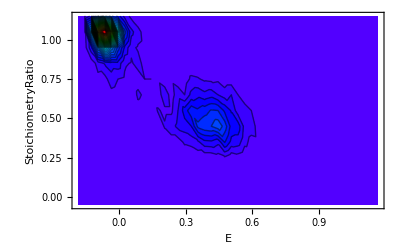

```mathematica
FSetPIEGamma[3.2]
FParamHisto2D["E","StoichiometryRatio",{-0.2,1.2,.03},{-0.1,1.2,0.1},PlotRange->All,Contours->40,ColorFunction->(If[#≠0,Hue[(0.73-.73#)],Hue[0.72]]&)]
```

1

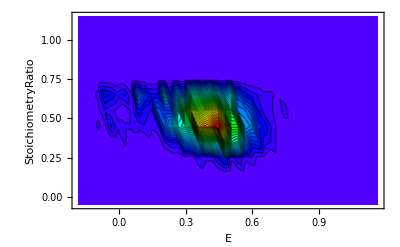

```mathematica
FSelectBursts[{"StoichiometryRatio"},(#[[1]]<0.7)&]

FParamHisto2D["E","StoichiometryRatio",{-0.2,1.2,.03},{-0.1,1.2,0.1},PlotRange->All,Contours->40,ColorFunction->(If[#≠0,Hue[(0.73-.73#)],Hue[0.72]]&),FBurstData->FSelectedBursts]
```

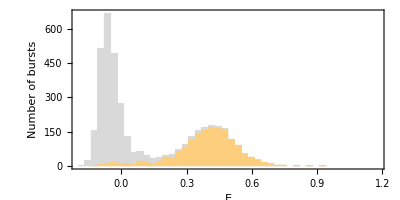

```mathematica
Show[{FParamHisto["E",{-0.2,1.2,0.03},ChartStyle->LightGray],FParamHisto["E",{-0.2,1.2,0.03},FBurstData->FSelectedBursts]}]
```

3.2

{1030.48,2373.97,17.1608,14.6691,0.,0.}

1599

{1050.52,2429.64,17.159,14.6768,0.,0.}

6450

{1017.02,2407.09,17.1698,14.6653,0.,0.}

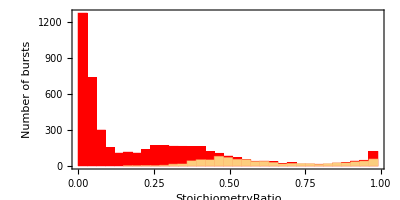

```mathematica
FSetPIEGamma[3.2]
FDetermineBackground[]
FFindBurstsFromTimeBinnedData[1,20,80,10000,FCombineContiguousBins->True,FPIEBurstIdentificationMethod->FMainChannelAboveThreshold]
FDetermineBackground[]
pl1=FParamHisto["StoichiometryRatio",{-0.0,1.0,0.03}];
FFindBurstsFromTimeBinnedData[1,20,80,10000,FCombineContiguousBins->True,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
FDetermineBackground[]
pl2=FParamHisto["StoichiometryRatio",{-0.0,1.0,0.03},ChartStyle->Red];
Show[pl2,pl1]
```

“BurstPIEAsymmetry”, FPIEBurstAsymmetry,  FPIECutAsymmetricBursts

4086

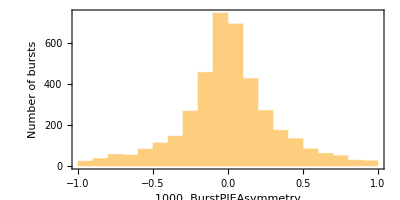

```mathematica
FFindBurstsDeltaT[0.00015,50,10000]
FParamHisto["BurstPIEAsymmetry"*1000.,{-1,1,0.1}]
```

3.2

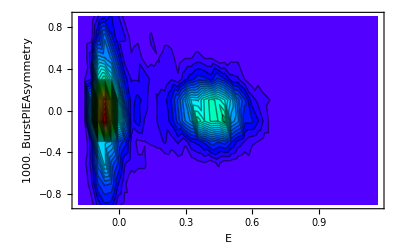

```mathematica
FSetPIEGamma[3.2]
FParamHisto2D["E","BurstPIEAsymmetry"*1000.,{-0.2,1.2,.03},{-1,1,0.2},PlotRange->All,Contours->40,ColorFunction->(If[#≠0,Hue[(0.73-.73#)],Hue[0.72]]&)]
```

```mathematica
?FPIEBurstAsymmetry
```

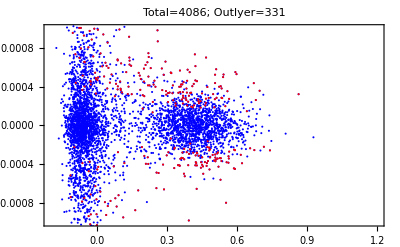
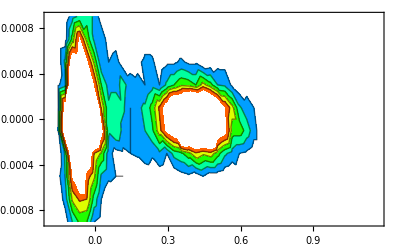
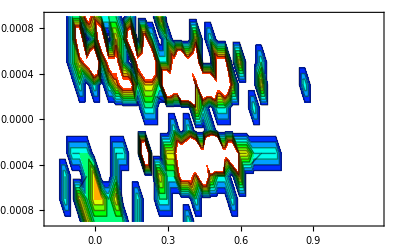

```mathematica
FPIEBurstAsymmetry[{-0.2,1.2,.03},{-0.001,0.001,0.0002},2.]
```

```mathematica
?FPIECutAsymmetricBursts
```

4086

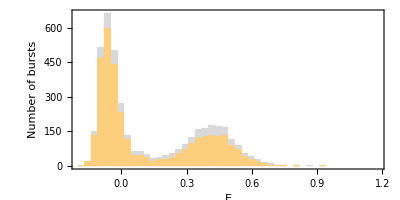

```mathematica
FFindBurstsDeltaT[0.00015,50,10000]
beforecut=FParamHisto["E",{-0.2,1.2,0.03},ChartStyle->LightGray];
FPIECutAsymmetricBursts[1.5];
aftercut=FParamHisto["E",{-0.2,1.2,0.03}];
Show[{beforecut,aftercut}]
```

| Related Guides
▪Fretica